```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={ψ[x]∈Reals};
```

```mathematica
e[x_]:={Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ψ'[x]}}

```mathematica
b[x_]:={{-ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-1/2 ψ'[x]

```mathematica
H[x_]:=-1/2 ψ'[x]
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:={{{0}}}
```

```mathematica
(*parameters*)
```

```mathematica
κ=1;
ρ=1;
η=1;
σc=1;
xmin=1;
xmax=3;
vmin=1;
wmin=0;
wmax=0;
sigmamax=1;
ψmin=1;
ψmax=2.5;
ψpmin=-1;
X1min=0;
X2min=0;
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.5},{2.9,2.30735},{2.8,2.11457},{2.7,1.92521},{2.6,1.74267},{2.5,1.56997},{2.4,1.40969},{2.3,1.26389},{2.2,1.13412},{2.1,1.02149},{2.,0.926726},{1.9,0.850254},{1.8,0.792311},{1.7,0.753},{1.6,0.732357},{1.5,0.730388},{1.4,0.747092},{1.3,0.782467},{1.2,0.836485},{1.1,0.909062},{1.,1.}}

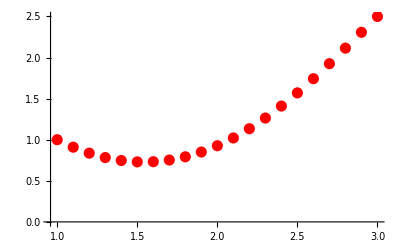

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

```mathematica
Show[plotψnum]
```

-Graphics-

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{0.649228,-1.61512},{0.723164,-1.54793},{0.782838,-1.4678},{0.826186,-1.37778},{0.852122,-1.28129},{0.860579,-1.18172},{0.852399,-1.08212},{0.829115,-0.984926},{0.792688,-0.891842},{0.745263,-0.803839},{0.688974,-0.721212},{0.625819,-0.643698},{0.557595,-0.570596},{0.485895,-0.500894},{0.412137,-0.43337},{0.337618,-0.366684},{0.263594,-0.299451},{0.191347,-0.230315},{0.122264,-0.158023},{0.0578972,-0.0815096},{0.,0.}}

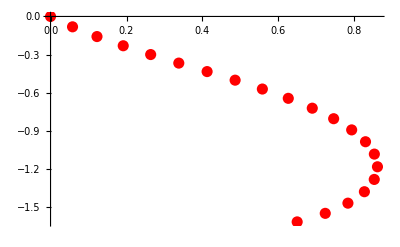

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

```mathematica
Show[plotXnum]
```

-Graphics-

```mathematica
(*plot the normal to the manifold n*)
```

```mathematica
(*tn=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/n.csv"];
tn=Table[{tn[[i,1]],tn[[i,2]]},{i,2,Length[tn]}]*)
```

```mathematica
(*plotn=Graphics[{Red,Table[Arrow[{{tX[[i,1]],tX[[i,2]]},{tX[[i,1]]+0.1*tn[[i,1]],tX[[i,2]]+0.1*tn[[i,2]]}}],{i,1,Length[t]}]},Frame->True,AspectRatio->1,PlotRange->All]*)
```